# Лабораторная работа 1 Жук Владислав, ПО-4

# 1.1 1. Используя функцию Range создайте список {1,2,3,4} Range[4]

{1,2,3,4}

```mathematica
2. Создайте список из натуральных чисел от 1 до 100 
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
3. Используя функции Range и Reverse,создайте список {4,3,2,1}
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
5. Используя функции Range,Reverse и Join,создайте список {1,2,3,4,4,3,2,1}
```

```mathematica
list = Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

```mathematica
6. Нарисовать график списка чисел,которые возрастают от 1 до 100,а затем убывают от 100
до 1
```

```mathematica
(*ListPlot - построение графика по точкам*)
```

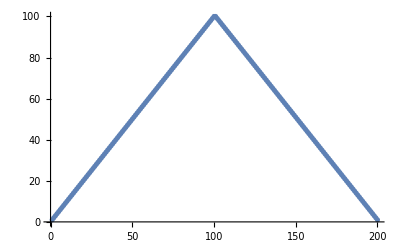

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]]
```

```mathematica
7. Используя функции Range и RandomInteger создайте список случайно генерированной
длины не превышающей число 10
```

```mathematica
(*RandomInteger[{a,b}] - дает случайное целое число в диапазоне {a,b}*)
```

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4}

```mathematica
8. Найти простейшую форму для команды Reverse[Reverse[Range[10]]
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]
```

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]
```

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
11. Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]
```

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
1.2
```

```mathematica
1. Присоедините две копии строки «Здравствуйте».
```

```mathematica
(*StringJoin - объединение двух и более строк*)
StringJoin["Здравствуйте ","Здравствуйте"]
```

Здравствуйте Здравствуйте

```mathematica
2. Создайте единую строку всего английского алфавита заглавными буквами
```

```mathematica
(*ToUpperCase - представляет все символы в строке заглавными буквами
Alphabet[] - дает список строчных букв от a до z в английском алфавите*)
```

```mathematica
ToUpperCase[Alphabet[]]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
3. Сгенерируйте строку английского алфавита в обратном порядке
```

```mathematica
Reverse[Alphabet[]]
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

```mathematica
4. Объедините 100 копий строки «ABCD»
```

```mathematica
(*StringRepeat["str",n] - создает строку,состоящую из "str",повторенных n раз.*)
```

```mathematica
StringJoin[StringRepeat["ABCD", 100]]
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

```mathematica
5. Используйте StringTake,StringJoin и Alphabet,чтобы получить «abcdef»
```

```mathematica
(*StringTake["string",n] - дает строку,содержащую первые n символов в «string».*)
```

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
6. Создайте столбец с числом элементов,равных длине строки «это о строках» и содержащих
число букв (включая пробелы) равное номеру элемент
```

```mathematica
(*Table[expr,{i,max}] - генерирует список значений expr,когда i работает от 1 до [i,max].
Column[{Subscript[expr, 1],Subscript[expr, 2],…}] - это объект,который форматируется с помощью[expr,i],расположенного в столбце,с [expr,1] над [expr,2] и т.д.*)
Column[Table[StringTake["это о строках",n],{n,StringLength["это о строках"]}]]
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

```mathematica
7. Создайте гистограмму длин слов в «Давным-давно,в далекой галактике,далеко»
```

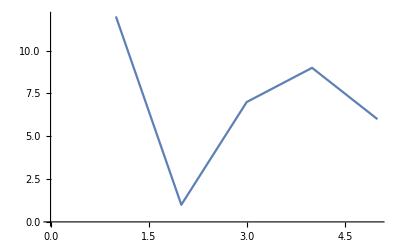

```mathematica
(*ListLinePlot - соединяет линиями точки
TextWords - дает список последовательностей символов,идентифицированных как слова в строке.*)
ListLinePlot[StringLength[TextWords["Давным-давно, в далёкой галактике, далеко"]]]
```

```mathematica
8. Найдите максимальную длину слова среди английских слов из WordList[]
```

```mathematica
(*WordList - дает список общеупотребительных слов.*)
```

```mathematica
WordList[]
```

{ага,ада,арф,бар,бас,бег,без,бей,бил,бит,31781,полуюмористическое,сверхъестественные,распространявшемуся,сверхъестественному,лесовостановительных,недоброжелательности,председательствовать,предусмотрительность,лесовосстановительных,предводительствуемыми}
 |  |  |  |

```mathematica
9. Используйте Length,чтобы найти длину русского алфавита
```

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.
```

```mathematica
StringJoin[Reverse[ToUpperCase[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

```mathematica
1.3
```

```mathematica
1. Используйте Range и чистую функцию для создания списка из квадратов первых 20
натуральных чисел
```

```mathematica
#^2 &/@Range[20]
```

```mathematica
{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

2. Составьте список из результатов смешивания желтого,зеленого и синего цветов с красным
цветом
```

```mathematica
(*Blind[{Subscript[col, 1],Subscript[col, 2]},x] - дает цвет,полученный путем смешивания дроби 1-x цвета col1 и x цвета col2].*)
Blend[{#,Red} ,1/2] &/@{Yellow, Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
3. Создайте список столбцов в рамках,содержащих прописные и строчные версии каждой
буквы алфавита
```

```mathematica
Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
4. Составьте список букв алфавита в случайных цветах в рамках,имеющих случайные цвета
фона.
```

```mathematica
Framed[Style[#, RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
5. Напишите в более простой форме команду (#^2+1&)/@Range[10].
```

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
1.4
```

```mathematica
1. Составьте список результатов использования функции Blur до 10 раз,начиная с
растрированного размера 30 “X” (Используйте:Rasterize[Style)
```

```mathematica
(*NestList[f, expr, n] - дает список результатов применения f к expr от 0 до n раз.
Rasterize[expr,elem] - дает элемент elem,связанный с растеризованной формой expr.
RasterSize - это параметр для растеризации и связанных с ним функций,который определяет абсолютный размер генерируемого растра в пикселях.*)
NestList[Blur,Rasterize[X,RasterSize->30],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
2. Начните с x,затем создайте список,использовав последовательно функцию Framed до 10
раз,используя каждый раз случайный цвет фона
```

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
3. Начните с размера 50 для “A”,затем создайте список вложенного применения Framed и
случайного вращения 5 раз.
```

```mathematica
(*FontSize - размер шрифта*)
NestList[Rotate[Framed[#],Pi * Random[]] &,Style["А",FontSize->50],5]
```

{А,А,А,А,А,А}

```mathematica
4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-#)&,начиная с 0.2
```

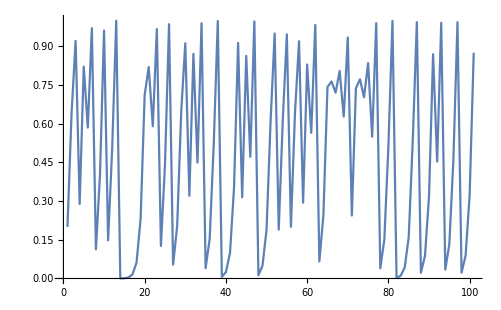

```mathematica
ListLinePlot[NestList[4#(1-#) &,0.2,100]]
```

```mathematica
5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&,начиная с 1
```

```mathematica
Nest[1+1/# &,1,30]
```

2178309/1346269

```mathematica
6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения.
```

```mathematica
NestList[3*# &,1,10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
7. Составьте список результатов действия вложенной функции (метод Ньютона) (#+2/#)/2 до
5 раз,начиная с 1.0,а затем вычтите корень 2 из всех результатов.
```

```mathematica
list=NestList[(#+2/#) /2  &,1.0,5]
#-Sqrt[2]&/@list
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421}

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

```mathematica
8. Создайте список из 5 степеней числа 2,т.е.2^2^2...^2 n раз,причем n меняется от 0 до 4.
```

```mathematica
NestList[#^2&,2,RandomInteger[4]]
```

{2,4,16,256}

```mathematica
1.5
1. Определите функцию f,которая вычисляет квадрат ее аргумента.
```

```mathematica
g[n_Integer]:= n^2
g[3]
```

9

```mathematica
2. Определите функцию poly,которая имеет целочисленное значение аргумента и создает
изображение оранжевого правильного многоугольника с числом сторон,равным значению
этого аргумента.
```

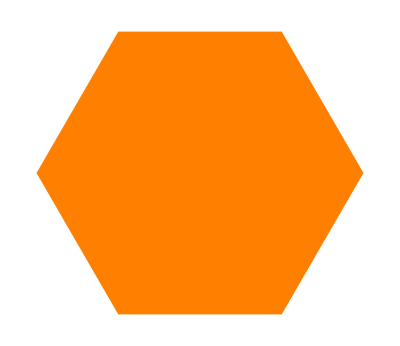

```mathematica
(*Graphics - представляет собой двумерное графическое изображение.*)
poly[n_Integer]:= Graphics[{Orange,Polygon[CirclePoints[n]]}]
poly[6]
```

```mathematica
3. Определите функцию f,которая берет список из двух элементов и помещает их в обратном
порядке
```

```mathematica
f[n_]:=Reverse[n]
f[{4,7}]
```

{7,4}

```mathematica
4. Определите функцию f,которая имеет два аргумента и дает результат в виде дроби,где
числитель равен произведению этих элементов,а знаменатель-их сумме.
```

```mathematica
f[n_,x_]:= (n*x)/(x+n)
f[3,7]
```

21/10

```mathematica
5. Определите функцию f,которая имеет два аргумента и дает результат в виде списка трех
элементов,которые соответственно равны сумме,разности и частному этих аргументов.
```

```mathematica
f[n_,x_]:= {n+x,n-x,n/x}
f[10,2]
```

{12,8,5}

```mathematica
6. Определите функцию evenodd,которая зависит от одного целочисленного аргумента и
имеет значение Black,если ее аргумент четный,значение-White в противном случае,значение
Red-если аргумент равен нулю.
```

```mathematica
(*If[condition,t,f] - дает t,если условие оценивается как True,и f,если оно оценивается как False.
EvenQ - возвращает True,если expr является четным целым числом,и False в противном случае.*)
evenodd[n_Integer]:= If[n!=0,If[EvenQ[n],Black,White],Red]
evenodd[3]
```

GrayLevel[1]

```mathematica
7. Определите функцию Fibonacci f с f[0]=1 и f[1]=1,а f[n] для натурального числа n является
суммой f[n-1] и f[n-2].
```

```mathematica
f[0] = 1;
f[1]=1;
f[n_]:= f[n-1] + f[n-2]
f[10]
Fibonacci[10]
```

55

55